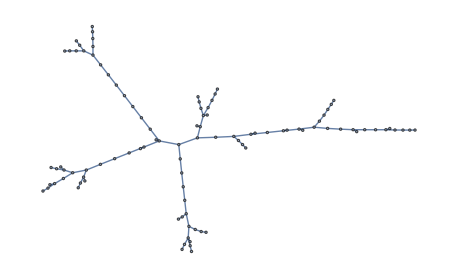

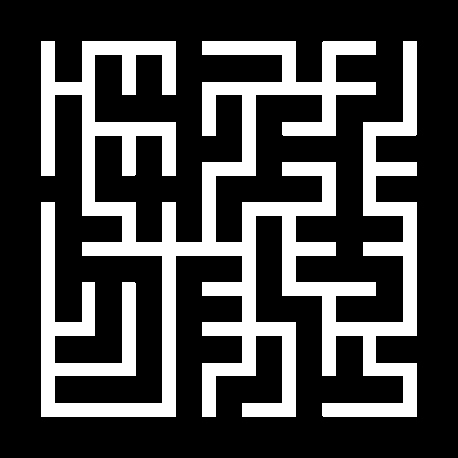

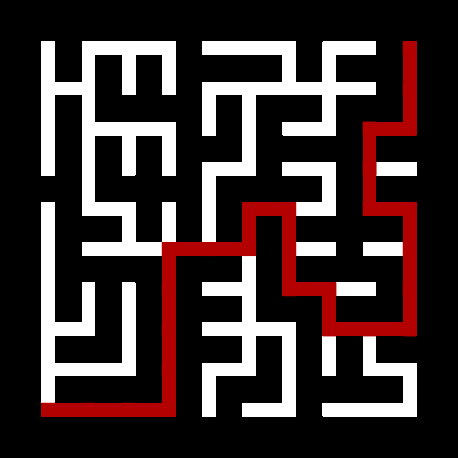

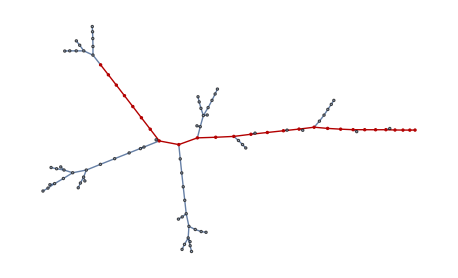

```mathematica
(*custom styling*)
n=10;
style={Background->GrayLevel[0],BaseStyle->{Directive[White,EdgeForm[],Opacity[1]]},VertexShapeFunction->(Rectangle[#1+.16,#1-.16]&),EdgeShapeFunction->(Rectangle[#1[[1]]+.16,#1[[2]]-.16]&)};
embedding=GraphEmbedding[GridGraph[{n,n}]];
g=GridGraph[{n,n},EdgeWeight->RandomReal[10,-2 n+2 n^2]];
tree=FindSpanningTree[{g,1}]
maze=Graph[tree,VertexCoordinates->embedding,style]
HighlightGraph[maze,PathGraph[FindShortestPath[maze,1,n^2]]]
HighlightGraph[tree,PathGraph[FindShortestPath[tree,1,n^2]]]
```

```mathematica
BarcodeImage[RandomReal[9,200]//ToString,"QR"]
```

-Graphics-

```mathematica
(*外极权二维元胞自动机*)
ArrayPlot[CellularAutomaton[{746,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{{Table[1,{7}]},0},{{{200}}}]]
```

-Graphics-

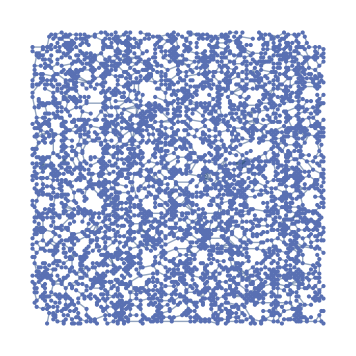

```mathematica
MorphologicalGraph[-Graphics-]
```

```mathematica
Sqrt
```